```mathematica
readHDF5Beam[filename_,opts___Rule]:=Block[{unrotate,verbose,cols,startposition,rotation},
unrotate=Global`HDF5Normalise/.{opts}/.{Global`HDF5Normalise->True};
verbose=Global`HDF5Verbose/.{opts}/.{Global`HDF5Verbose->False};
cols=Import[filename,"/beam/columns"];
Clear[Evaluate[#]]&/@cols;
beamdata=Transpose[Import[filename,"/beam/beam"]];
startposition=Import[filename,"/Parameters/Starting_Position"];
rotation=Import[filename,"/Parameters/Rotation"];
If[unrotate,
beamdata[[{1,2,3}]]=Transpose[(#-startposition&/@Transpose[beamdata[[{1,2,3}]]]).RotationMatrix[rotation,{0,1,0}]];
beamdata[[{4,5,6}]]=Transpose[((#&/@Transpose[beamdata[[{4,5,6}]]]).RotationMatrix[rotation,{0,1,0}])];
];
MapThread[(Evaluate[Symbol@#1]=#2)&,{cols,beamdata}];
params=Import[filename,"/Parameters"];
Clear[Evaluate[StringReplace[#1,{"_"->"£","-"->"$"}]]]&/@Keys[params];
MapThread[(Evaluate[Symbol@StringReplace[#1,{"_"->"£","-"->"$"}]]=#2)&,{Keys[params],Values[params]}];
If[verbose,
Print["Parameter(s) Assigned: ",Keys[params]];
Print["Variables(s) Assigned: ",cols];
];
]
```

```mathematica
Block[{no=#},
dir="TOMP_SC_"<>ToString[no];
CreateDirectory["C:\\Users\\jkj62.CLRC\\SynologyDrive\\TomPacey\\SC"];
CreateDirectory["C:\\Users\\jkj62.CLRC\\SynologyDrive\\TomPacey\\SC\\"<>dir];
CopyFile["\\\\apclara1\\jkj62\\Github\\OnlineModel\\SimulationFramework\\Examples\\CLARA_BA1\\"<>dir<>"\\EBT-INJ-DIA-YAG-05.hdf5","C:\\Users\\jkj62.CLRC\\SynologyDrive\\TomPacey\\SC\\"<>dir<>"\\EBT-INJ-DIA-YAG-05.hdf5",OverwriteTarget->True];
CopyFile["\\\\apclara1\\jkj62\\Github\\OnlineModel\\SimulationFramework\\Examples\\CLARA_BA1\\"<>dir<>"\\EBT-BA1-COFFIN-FOC.hdf5","C:\\Users\\jkj62.CLRC\\SynologyDrive\\TomPacey\\SC\\"<>dir<>"\\EBT-BA1-COFFIN-FOC.hdf5",OverwriteTarget->True];
]&/@Range[-25,25]
```

CreateDirectory::filex: C:\Users\jkj62.CLRC\SynologyDrive\TomPacey\TOMP_SC_-25 already exists.

CreateDirectory::filex: C:\Users\jkj62.CLRC\SynologyDrive\TomPacey\TOMP_SC_-24 already exists.

CreateDirectory::filex: C:\Users\jkj62.CLRC\SynologyDrive\TomPacey\TOMP_SC_-23 already exists.

General::stop: Further output of CreateDirectory::filex will be suppressed during this calculation.

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
Block[{no=#},
dir="TOMP_NoSC_"<>ToString[no];
CreateDirectory["C:\\Users\\jkj62.CLRC\\SynologyDrive\\TomPacey\\NoSC"];
CreateDirectory["C:\\Users\\jkj62.CLRC\\SynologyDrive\\TomPacey\\NoSC\\"<>dir];
CopyFile["\\\\apclara1\\jkj62\\Github\\OnlineModel\\SimulationFramework\\Examples\\CLARA_BA1\\"<>dir<>"\\EBT-INJ-DIA-YAG-05.hdf5","C:\\Users\\jkj62.CLRC\\SynologyDrive\\TomPacey\\NoSC\\"<>dir<>"\\EBT-INJ-DIA-YAG-05.hdf5",OverwriteTarget->True];
CopyFile["\\\\apclara1\\jkj62\\Github\\OnlineModel\\SimulationFramework\\Examples\\CLARA_BA1\\"<>dir<>"\\EBT-BA1-COFFIN-FOC.hdf5","C:\\Users\\jkj62.CLRC\\SynologyDrive\\TomPacey\\NoSC\\"<>dir<>"\\EBT-BA1-COFFIN-FOC.hdf5",OverwriteTarget->True];
]&/@Range[-25,25]
```

CreateDirectory::filex: C:\Users\jkj62.CLRC\SynologyDrive\TomPacey\NoSC already exists.

General::stop: Further output of CreateDirectory::filex will be suppressed during this calculation.

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
Block[{no=#},
dir="TOMP_ASTRA_"<>ToString[no];
CreateDirectory["C:\\Users\\jkj62.CLRC\\SynologyDrive\\TomPacey\\ASTRA"];
CreateDirectory["C:\\Users\\jkj62.CLRC\\SynologyDrive\\TomPacey\\ASTRA\\"<>dir];
CopyFile["\\\\apclara1\\jkj62\\Github\\OnlineModel\\SimulationFramework\\Examples\\CLARA_BA1\\"<>dir<>"\\EBT-INJ-DIA-YAG-05.hdf5","C:\\Users\\jkj62.CLRC\\SynologyDrive\\TomPacey\\ASTRA\\"<>dir<>"\\EBT-INJ-DIA-YAG-05.hdf5",OverwriteTarget->True];
CopyFile["\\\\apclara1\\jkj62\\Github\\OnlineModel\\SimulationFramework\\Examples\\CLARA_BA1\\"<>dir<>"\\EBT-BA1-COFFIN-FOC.hdf5","C:\\Users\\jkj62.CLRC\\SynologyDrive\\TomPacey\\ASTRA\\"<>dir<>"\\EBT-BA1-COFFIN-FOC.hdf5",OverwriteTarget->True];
]&/@Range[-25,25]
```

Near data:

```mathematica
readHDF5Beam["\\\\apclara1\\jkj62\\Github\\OnlineModel\\SimulationFramework\\Examples\\CLARA_BA1\\TOMP_SC_-12\\EBT-INJ-DIA-YAG-05.hdf5",HDF5Verbose->True]
```

Parameter(s) Assigned: {Rotation,Source,Starting_Position,centered,code,npart,particle_mass,total_charge}

Variables(s) Assigned: {x,y,z,cpx,cpy,cpz,t,q}

Far data:

```mathematica
nearplot=ListPlot[{Transpose[{10^15(t-Mean[t]),10^-6 cpz}]}];
```

```mathematica
dataNear=Transpose[{10^15(t-Mean[t]),10^-6 cpz}];
```

```mathematica
readHDF5Beam["\\\\apclara1\\jkj62\\Github\\OnlineModel\\SimulationFramework\\Examples\\CLARA_BA1\\TOMP_SC_-12\\EBT-BA1-COFFIN-FOC.hdf5",HDF5Verbose->True]
```

Parameter(s) Assigned: {Rotation,Source,Starting_Position,centered,code,npart,particle_mass,total_charge}

Variables(s) Assigned: {x,y,z,cpx,cpy,cpz,t,q}

```mathematica
total£charge
```

6.5534×10^-11

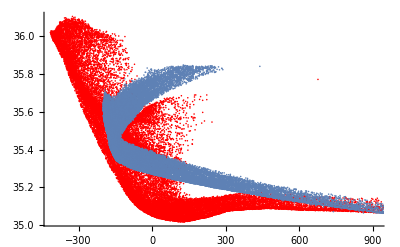

```mathematica
Show[ListPlot[{Transpose[{10^15(t-Mean[t]),10^-6 cpz}]},PlotStyle->Red],nearplot]
```

```mathematica
dataFar=Transpose[{10^15(t-Mean[t]),10^-6 cpz}];
```

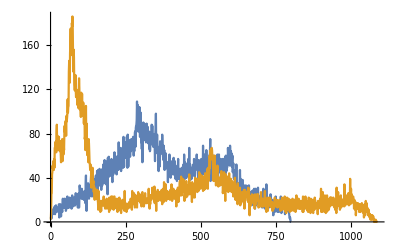

```mathematica
ListLinePlot[{
BinCounts[dataNear,{-10^6,10^6,2 10^6},{Min[dataNear[[All,2]]],Max[dataNear[[All,2]]],0.001}][[1]],
BinCounts[dataFar,{-10^6,10^6,2 10^6},{Min[dataFar[[All,2]]],Max[dataFar[[All,2]]],0.001}][[1]]},PlotRange->All]
```

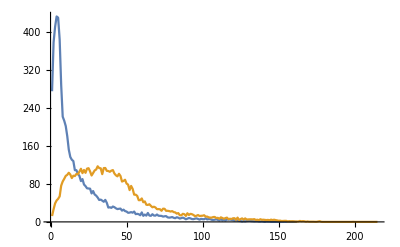

```mathematica
ListLinePlot[{
(# Abs[total£charge])/(Length[x] 10 10^-15)&/@Flatten[BinCounts[dataNear,{Min[dataNear[[All,1]]],Max[dataNear[[All,1]]],10},{-0,100,100}],1],
(# Abs[total£charge])/(Length[x] 10 10^-15)&/@Flatten[BinCounts[dataFar,{Min[dataFar[[All,1]]],Max[dataFar[[All,1]]],10},{-0,100,100}],1]},PlotRange->All]
```

## ASTRA

```mathematica
<<ASTRAInterpret`
```

```mathematica
dir="TOMP_ASTRA_-11";
```

```mathematica
ASTRABeamInterpret["\\\\apclara1\\jkj62\\Github\\OnlineModel\\SimulationFramework\\Examples\\CLARA_BA1\\"<>dir<>"\\S02.2443.001",ASTRAVerbose->True]
```

Columns Redefined: x [m], y [m], z [m], px [eV/c], py [eV/c], pz [eV/c], clock [ns], charge [nC], index [DimensionlessUnit], status [DimensionlessUnit]

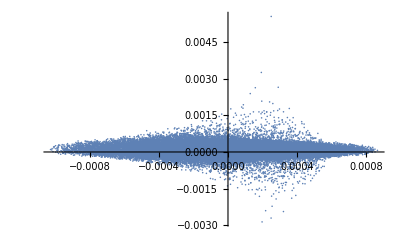

```mathematica
ListPlot[{Transpose[{x-Mean[x],y}]},PlotRange->All]
```

```mathematica
speedoflight=QuantityMagnitude[UnitConvert[Quantity["SpeedOFlight"]]]
```

299792458

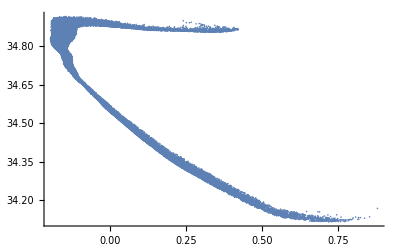

```mathematica
ListPlot[{Transpose[{-10^12(z-Mean[z])/speedoflight,10^-6 pz}]},PlotRange->All]
```

```mathematica
ASTRAemitInterpret[{"\\\\apclara1\\jkj62\\Github\\OnlineModel\\SimulationFramework\\Examples\\CLARA_BA1\\"<>dir<>"\\S02.Xemit.001"},ASTRAVerbose->True]
```

Columns Redefined: z [m], t [ns], xavr [mm], xrms [mm], xprms [mrad], ϵxnorm [mm mrad π], xxpavr [mm mrad]

Columns Redefined: z [m], t [ns], yavr [mm], yrms [mm], yprms [mrad], ϵynorm [mm mrad π], yypavr [mm mrad]

Columns Redefined: z [m], t [ns], Ekin [MeV], zrms [mm], ΔErms [keV], ϵznorm [keV mm π], zEavr [keV]

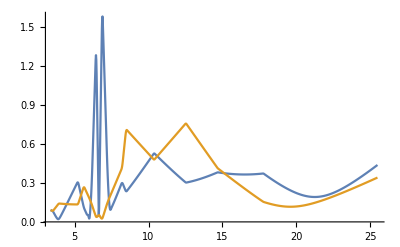

```mathematica
ListLinePlot[{Transpose[{z,xrms}],Transpose[{z,yrms}]},PlotRange->All]
```

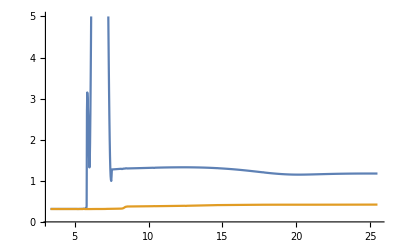

```mathematica
ListLinePlot[{Transpose[{z,ϵxnorm}],Transpose[{z,ϵynorm}]},PlotRange->{All,{0,5}}]
```

## Elegant

```mathematica
<<sddsInterpret`
```

```mathematica
dir="TOMP_SC_15"
```

TOMP_SC_15

```mathematica
sddsInterpret["\\\\apclara1\\jkj62\\Github\\OnlineModel\\SimulationFramework\\Examples\\CLARA_BA1\\"<>dir<>"\\EBT-INJ-DIA-YAG-05.SDDS"]
```

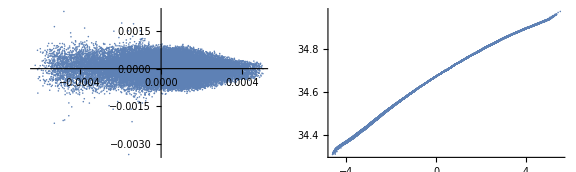

```mathematica
GraphicsGrid[{{ListPlot[{Transpose[{x-Mean[x],y}]},PlotRange->All],ListPlot[{Transpose[{10^12(t-Mean[t]),0.511p}]},PlotRange->All]}},ImageSize->Large]
```

```mathematica
sddsInterpret["\\\\apclara1\\jkj62\\Github\\OnlineModel\\SimulationFramework\\Examples\\CLARA_BA1\\"<>dir<>"\\EBT-BA1-COFFIN-FOC.SDDS"]
```

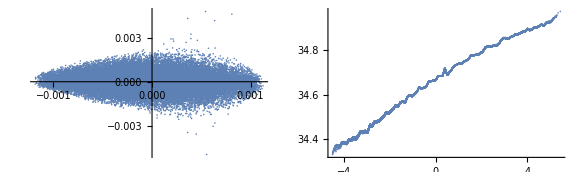

```mathematica
GraphicsGrid[{{ListPlot[{Transpose[{x-Mean[x],y}]},PlotRange->All],ListPlot[{Transpose[{10^12(t-Mean[t]),0.511p}]},PlotRange->All]}},ImageSize->Large]
```

```mathematica
lists=BinLists[Sort[Transpose[{t,0.511p}],#1[[1]]<#2[[1]]&],{Min[t],Max[t],0.1 10^-12},{0,1000,1000}];
```

```mathematica
Flatten[Differences/@MinMax/@lists[[All,1,All,-1]]]
```

{0.0356962,0.0314695,0.0216769,0.0254775,0.0122535,0.0131598,0.0216632,0.0121823,0.0179786,0.0136603,0.0200099,0.0238463,0.0135063,0.0121558,0.0122002,0.030544,0.0190772,0.0199117,0.0152621,0.00976483,0.0162501,0.0170437,0.0199221,0.0128204,0.0113722,0.0168161,0.0156516,0.0126464,0.0121576,0.0161183,0.00583117,0.0107603,0.0223565,0.00851387,0.00679895,0.012176,0.0135878,0.0164525,0.00660246,0.00579628,0.00831239,0.0202641,0.00302192,0.0044067,0.00263715,0.0178791,0.00291057,0.00200034,0.0319016,0.0284834,0.014713,0.0131934,0.0166343,0.0071283,0.00740033,0.0040296,0.00879066,0.0088239,0.00763052,0.0151438,0.00664111,0.00458258,0.00339327,0.00739008,0.0083976,0.0154842,0.014055,0.00547242,0.00398626,0.00601162,0.00635783,0.00614279,0.0140902,0.016257,0.00799198,0.00473045,0.00502611,0.00915634,0.00758639,0.00902379,0.00410592,0.00735576,0.00875292,0.00566206,0.0143329,0.00899431,0.0066857,0.0119301,0.00463012,0.00887104,0.00908079,0.00905974,0.0149853,0.00796844,0.00924796,0.0140559,0.0109443,0.0100661,0.}

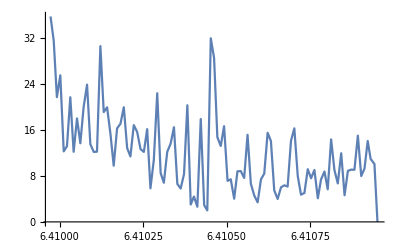

```mathematica
ListLinePlot[Transpose[{Mean/@lists[[All,1,All,1]], 10^3 Flatten[Differences/@MinMax/@lists[[All,1,All,-1]]]}]]
```

```mathematica
sddsInterpret["\\\\apclara1\\jkj62\\Github\\OnlineModel\\SimulationFramework\\Examples\\CLARA_BA1\\"<>dir<>"\\S02.twi",sddsVerbose->True]
```

Number of Pages: 1;	Current Page(s): {1}

Variables (Re)Assigned: {s, betax, alphax, psix, etax, etaxp, xAperture, betay, alphay, psiy, etay, etayp, yAperture, pCentral0, ElementName, ElementOccurence, ElementType, dI1, dI2, dI3, dI4, dI5}

Parameters (Re)Assigned: {Step, nux, dnuxdp, dnuxdp2, dnuxdp3, Ax, AxLocation, nuy, dnuydp, dnuydp2, dnuydp3, Ay, AyLocation, deltaHalfRange, nuxChromUpper, nuxChromLower, nuyChromUpper, nuyChromLower, Stage, pCentral, dbetaxdp, dbetaydp, dalphaxdp, dalphaydp, etax2, etay2, etax3, etay3, etaxp2, etayp2, etaxp3, etayp3, betaxMin, betaxAve, betaxMax, betayMin, betayAve, betayMax, etaxMax, etayMax, waistsx, waistsy, dnuxdAx, dnuxdAy, dnuydAx, dnuydAy, dnuxdAx2, dnuxdAy2, dnuxdAxAy, dnuydAx2, dnuydAy2, dnuydAxAy, nuxTswaLower, nuxTswaUpper, nuyTswaLower, nuyTswaUpper, couplingIntegral, couplingDelta, emittanceRatio, alphac2, alphac, I1, I2, I3, I4, I5, ex0, enx0, taux, Jx, tauy, Jy, Sdelta0, taudelta, Jdelta, U0}

```mathematica
sddsInterpret["\\\\apclara1\\jkj62\\Github\\OnlineModel\\SimulationFramework\\Examples\\CLARA_BA1\\"<>dir<>"\\S02.mat",sddsVerbose->True]
```

Number of Pages: 1;	Current Page(s): {1}

Variables (Re)Assigned: {s, ElementName, ElementOccurence, ElementType, C1, C2, C3, C4, C5, C6, R11, R12, R13, R14, R15, R16, R21, R22, R23, R24, R25, R26, R31, R32, R33, R34, R35, R36, R41, R42, R43, R44, R45, R46, R51, R52, R53, R54, R55, R56, R61, R62, R63, R64, R65, R66}

Parameters (Re)Assigned: {Step}

```mathematica
R56[[-1]]
```

0.0773978

```mathematica
0.002/0.37
```

0.00540541

```mathematica
0.0054*R56[[-1]]
```

0.000417948

```mathematica
10^12(0.001/0.37)*R56[[-1]]/(3 10^8)
```

0.697278

```mathematica
R56[[-1]]*0.0005/0.368412
```

0.000105042

```mathematica
0.005/0.367
```

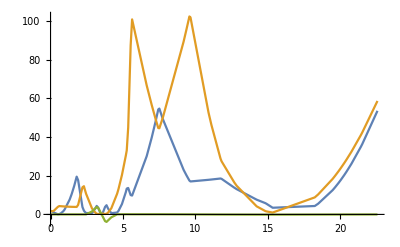

```mathematica
ListLinePlot[{Transpose[{s,betax}],Transpose[{s,betay}],Transpose[{s,10etax}]},PlotRange->All]
```

```mathematica
ElementName
```

{_BEG_,START,CLA-S02-APER-01,CLA-S02-MAG-HVCOR-01,DRIFT1,CLA-S02-MAG-QUAD-01,CLA-S02-DIA-BPM-01,DRIFT2,CLA-S02-MAG-QUAD-02,DRIFT3,CLA-S02-DIA-SCR-01-W,DRIFT4,CLA-S02-MAG-HVCOR-02,DRIFT5,CLA-S02-COL-01,CLA-S02-APER-02,DRIFT6,CLA-S02-MAG-HVCOR-03,DRIFT7,CLA-S02-DIA-SCR-02-W,DRIFT8,CLA-S02-MAG-QUAD-03,DRIFT9,CLA-S02-MAG-QUAD-04,DRIFT10,CLA-C2V-MARK-01,DRIFT11,CLA-C2V-MAG-DIP-01,DRIFT12,CLA-C2V-MAG-HVCOR-01,CLA-C2V-DIA-BPM-01,DRIFT13,CLA-C2V-MAG-QUAD-01,DRIFT14,CLA-C2V-MAG-QUAD-02,DRIFT15,CLA-C2V-MAG-QUAD-03,DRIFT16,CLA-C2V-DIA-SCR-01-W,DRIFT17,CLA-C2V-MAG-DIP-02,DRIFT18,CLA-C2V-MARK-02,DRIFT19,EBT-INJ-DIA-YAG-05,DRIFT20,EBT-INJ-MAG-HVCOR-06,EBT-INJ-MAG-QUAD-07,DRIFT21,EBT-INJ-MAG-QUAD-08,DRIFT22,EBT-INJ-DIA-YAG-06,DRIFT23,EBT-INJ-DIA-FCUP-02,DRIFT24,EBT-INJ-MAG-HVCOR-07,EBT-INJ-MAG-QUAD-09,EBT-INJ-DIA-BPM-04,DRIFT25,EBT-INJ-DIA-YAG-07,EBT-INJ-MAG-HVCOR-08,DRIFT26,EBT-INJ-MAG-QUAD-10,DRIFT27,EBT-INJ-DIA-BPM-05,DRIFT28,EBT-INJ-MAG-QUAD-11,DRIFT29,EBT-INJ-DIA-YAG-08,EBT-INJ-MAG-HVCOR-09,DRIFT30,EBT-INJ-DIA-ICT-03,EBT-INJ-DIA-YAG-10,DRIFT31,EBT-INJ-MAG-QUAD-15,DRIFT32,EBT-INJ-PSS-SHUT-02,DRIFT33,EBT-BA1-DIA-BPM-01,EBT-BA1-DIA-YAG-01,DRIFT34,EBT-BA1-MAG-QUAD-01,DRIFT35,EBT-BA1-MAG-QUAD-02,EBT-BA1-DIA-BPM-02,EBT-BA1-MAG-QUAD-03,DRIFT36,EBT-BA1-LASERBOX-BEG,DRIFT37,EBT-BA1-LASERBOX-END,DRIFT38,EBT-BA1-COFFIN-BEG,DRIFT39,EBT-BA1-COFFIN-FOC,END}

```mathematica
Transpose[{s,ElementName,etax}][[Position[ElementName,"CLA-C2V-DIA-BPM-01"][[1,1]]]]
```

{3.16545,CLA-C2V-DIA-BPM-01,0.368412}

```mathematica
100*0.001/0.36841227061810083
```

0.271435

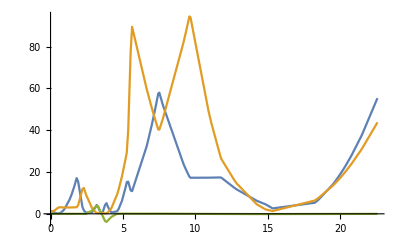

```mathematica
ListLinePlot[{Transpose[{s,betax}],Transpose[{s,betay}],Transpose[{s,10etax}]},PlotRange->All]
```

```mathematica
sddsInterpret["\\\\apclara1\\jkj62\\Github\\OnlineModel\\SimulationFramework\\Examples\\CLARA_BA1\\"<>dir<>"\\S02.sig",sddsVerbose->True]
```

Number of Pages: 1;	Current Page(s): {1}

Variables (Re)Assigned: {s, ElementName, ElementOccurence, ElementType, s1, s12, s13, s14, s15, s16, s17, s2, s23, s24, s25, s26, s27, s3, s34, s35, s36, s37, s4, s45, s46, s47, s5, s56, s57, s6, s67, s7, ma1, ma2, ma3, ma4, ma5, ma6, ma7, minimum1, minimum2, minimum3, minimum4, minimum5, minimum6, minimum7, maximum1, maximum2, maximum3, maximum4, maximum5, maximum6, maximum7, Sx, Sxp, Sy, Syp, Ss, Sdelta, St, ex, enx, ecx, ecnx, ey, eny, ecy, ecny, betaxBeam, alphaxBeam, betayBeam, alphayBeam}

Parameters (Re)Assigned: {Step}

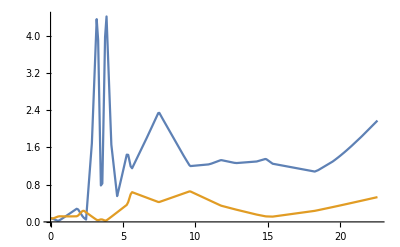

```mathematica
ListLinePlot[{Transpose[{s,10^3 Sx}],Transpose[{s,10^3 Sy}]}]
```

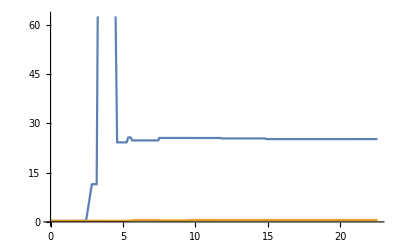

```mathematica
ListLinePlot[{Transpose[{s,10^6 enx}],Transpose[{s,10^6 eny}]}]
```

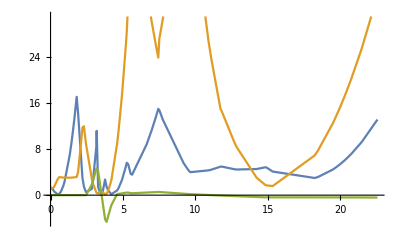

```mathematica
ListLinePlot[{Transpose[{s,betaxBeam}],Transpose[{s,betayBeam}],Transpose[{s,100000s16}]}]
```

## Elegant DBURT (apclara1)

```mathematica
<<sddsInterpret`
```

```mathematica
dir="TOMP_SC_DBURT_15"
```

TOMP_SC_DBURT_15

```mathematica
sddsInterpret["\\\\apclara1\\jkj62\\Github\\OnlineModel\\SimulationFramework\\Examples\\CLARA_BA1\\"<>dir<>"\\EBT-INJ-DIA-YAG-05.SDDS"]
```

FindList::noopen: Cannot open \\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\TOMP_SC_DBURT_15\EBT-INJ-DIA-YAG-05.SDDS.

ReadList::noopen: Cannot open \\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\TOMP_SC_DBURT_15\EBT-INJ-DIA-YAG-05.SDDS.

FindList::noopen: Cannot open \\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\TOMP_SC_DBURT_15\EBT-INJ-DIA-YAG-05.SDDS.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed,1].

Part::partd: Part specification Flatten[$Failed,1]⟦All,1⟧ is longer than depth of object.

Part::pkspec1: The expression Flatten[$Failed,1] cannot be used as a part specification.

ReadList::noopen: Cannot open \\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\TOMP_SC_DBURT_15\EBT-INJ-DIA-YAG-05.SDDS.

Part::pkspec1: The expression 1⟦All,Flatten[$Failed,1]⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦1⟦All,Flatten[$Failed,1]⟧⟧,{ →}].

StringTake::strse: String or list of strings expected at position 1 in StringTake[StringReplace[$Failed⟦1⟦All,Flatten[$Failed,1]⟧⟧,{ →}],-4].

StringInsert::strse: String or list of strings expected at position 1 in StringInsert[$Failed⟦1⟦All,Flatten[$Failed,1]⟧⟧,$Failed⟦1+1⟦All,Flatten[$Failed,1]⟧⟧,-1].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦1+1⟦All,Flatten[$Failed,1]⟧⟧,{ →}].

StringTake::strse: String or list of strings expected at position 1 in StringTake[StringReplace[$Failed⟦1+1⟦All,Flatten[$Failed,1]⟧⟧,{ →}],-4].

StringInsert::strse: String or list of strings expected at position 1 in StringInsert[StringInsert[$Failed⟦1⟦All,Flatten[$Failed,1]⟧⟧,$Failed⟦1+1⟦All,Flatten[$Failed,1]⟧⟧,-1],$Failed⟦2+1⟦All,Flatten[$Failed,1]⟧⟧,-1].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦2+1⟦All,Flatten[$Failed,1]⟧⟧,{ →}].

General::stop: Further output of StringReplace::strse will be suppressed during this calculation.

StringTake::strse: String or list of strings expected at position 1 in StringTake[StringReplace[$Failed⟦2+1⟦All,Flatten[$Failed,1]⟧⟧,{ →}],-4].

General::stop: Further output of StringTake::strse will be suppressed during this calculation.

StringInsert::strse: String or list of strings expected at position 1 in StringInsert[StringInsert[StringInsert[$Failed⟦1⟦All,Flatten[$Failed,1]⟧⟧,$Failed⟦1+1⟦All,Flatten[$Failed,1]⟧⟧,-1],$Failed⟦2+1⟦All,Flatten[$Failed,1]⟧⟧,-1],$Failed⟦3+1⟦All,Flatten[$Failed,1]⟧⟧,-1].

General::stop: Further output of StringInsert::strse will be suppressed during this calculation.

$Aborted

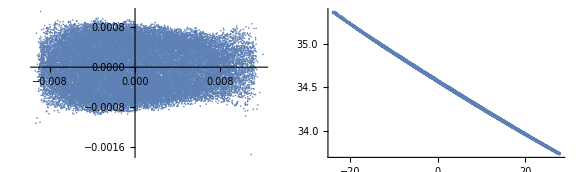

```mathematica
GraphicsGrid[{{ListPlot[{Transpose[{x-Mean[x],y}]},PlotRange->All],ListPlot[{Transpose[{10^12(t-Mean[t]),0.511p}]},PlotRange->All]}},ImageSize->Large]
```

```mathematica
sddsInterpret["C:\\anaconda32\\Work\\OnlineModel\\SimulationFramework\\Examples\\CLARA_BA1\\"<>dir<>"\\EBT-BA1-COFFIN-FOC.SDDS"]
```

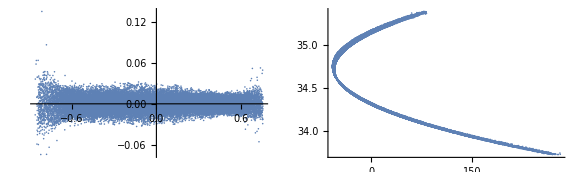

```mathematica
GraphicsGrid[{{ListPlot[{Transpose[{x,y}]},PlotRange->All],ListPlot[{Transpose[{10^12(t-Mean[t]),0.511p}]},PlotRange->All]}},ImageSize->Large]
```

```mathematica
sddsInterpret["C:\\anaconda32\\Work\\OnlineModel\\SimulationFramework\\Examples\\CLARA_BA1\\"<>dir<>"\\S02.twi",SDDSVerbose->True]
```

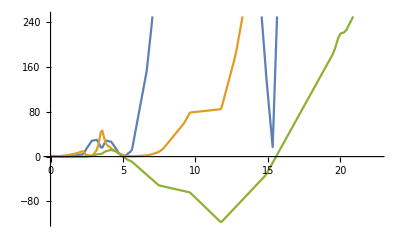

```mathematica
ListLinePlot[{Transpose[{s,betax}],Transpose[{s,betay}],Transpose[{s,10etax}]},PlotRange->{All,{Automatic,250}}]
```

```mathematica
sddsInterpret["C:\\anaconda32\\Work\\OnlineModel\\SimulationFramework\\Examples\\CLARA_BA1\\"<>dir<>"\\S02.sig",sddsVerbose->True]
```

Number of Pages: 1;	Current Page(s): {1}

Variables (Re)Assigned: {s, ElementName, ElementOccurence, ElementType, s1, s12, s13, s14, s15, s16, s17, s2, s23, s24, s25, s26, s27, s3, s34, s35, s36, s37, s4, s45, s46, s47, s5, s56, s57, s6, s67, s7, ma1, ma2, ma3, ma4, ma5, ma6, ma7, minimum1, minimum2, minimum3, minimum4, minimum5, minimum6, minimum7, maximum1, maximum2, maximum3, maximum4, maximum5, maximum6, maximum7, Sx, Sxp, Sy, Syp, Ss, Sdelta, St, ex, enx, ecx, ecnx, ey, eny, ecy, ecny, betaxBeam, alphaxBeam, betayBeam, alphayBeam}

Parameters (Re)Assigned: {Step}

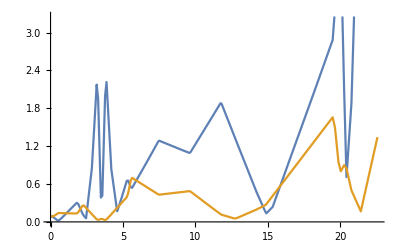

```mathematica
ListLinePlot[{Transpose[{s,10^3 Sx}],Transpose[{s,10^3 Sy}]}]
```

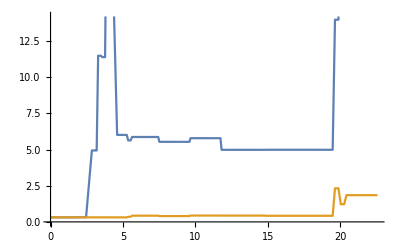

```mathematica
ListLinePlot[{Transpose[{s,10^6 enx}],Transpose[{s,10^6 eny}]}]
```

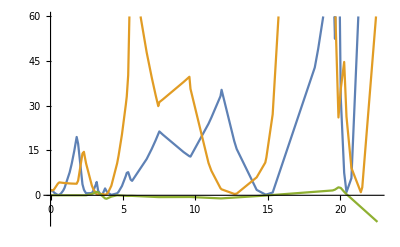

```mathematica
ListLinePlot[{Transpose[{s,betaxBeam}],Transpose[{s,betayBeam}],Transpose[{s,100000s16}]}]
```

## Elegant DBURT (local)

```mathematica
<<sddsInterpret`
```

```mathematica
dir="TOMP_SC_DBURT_15"
```

TOMP_SC_DBURT_15

```mathematica
sddsInterpret["C:\\anaconda32\\Work\\OnlineModel\\SimulationFramework\\Examples\\CLARA_BA1\\"<>dir<>"\\EBT-INJ-DIA-YAG-05.SDDS"]
```

FindList::noopen: Cannot open C:\anaconda32\Work\OnlineModel\SimulationFramework\Examples\CLARA_BA1\TOMP_SC_DBURT_15\EBT-INJ-DIA-YAG-05.SDDS.

ReadList::noopen: Cannot open C:\anaconda32\Work\OnlineModel\SimulationFramework\Examples\CLARA_BA1\TOMP_SC_DBURT_15\EBT-INJ-DIA-YAG-05.SDDS.

FindList::noopen: Cannot open C:\anaconda32\Work\OnlineModel\SimulationFramework\Examples\CLARA_BA1\TOMP_SC_DBURT_15\EBT-INJ-DIA-YAG-05.SDDS.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed,1].

Part::partd: Part specification Flatten[$Failed,1]⟦All,1⟧ is longer than depth of object.

Part::pkspec1: The expression Flatten[$Failed,1] cannot be used as a part specification.

ReadList::noopen: Cannot open C:\anaconda32\Work\OnlineModel\SimulationFramework\Examples\CLARA_BA1\TOMP_SC_DBURT_15\EBT-INJ-DIA-YAG-05.SDDS.

Part::pkspec1: The expression 1⟦All,Flatten[$Failed,1]⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦1⟦All,Flatten[$Failed,1]⟧⟧,{ →}].

StringTake::strse: String or list of strings expected at position 1 in StringTake[StringReplace[$Failed⟦1⟦All,Flatten[$Failed,1]⟧⟧,{ →}],-4].

StringInsert::strse: String or list of strings expected at position 1 in StringInsert[$Failed⟦1⟦All,Flatten[$Failed,1]⟧⟧,$Failed⟦1+1⟦All,Flatten[$Failed,1]⟧⟧,-1].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦1+1⟦All,Flatten[$Failed,1]⟧⟧,{ →}].

StringTake::strse: String or list of strings expected at position 1 in StringTake[StringReplace[$Failed⟦1+1⟦All,Flatten[$Failed,1]⟧⟧,{ →}],-4].

StringInsert::strse: String or list of strings expected at position 1 in StringInsert[StringInsert[$Failed⟦1⟦All,Flatten[$Failed,1]⟧⟧,$Failed⟦1+1⟦All,Flatten[$Failed,1]⟧⟧,-1],$Failed⟦2+1⟦All,Flatten[$Failed,1]⟧⟧,-1].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦2+1⟦All,Flatten[$Failed,1]⟧⟧,{ →}].

General::stop: Further output of StringReplace::strse will be suppressed during this calculation.

StringTake::strse: String or list of strings expected at position 1 in StringTake[StringReplace[$Failed⟦2+1⟦All,Flatten[$Failed,1]⟧⟧,{ →}],-4].

General::stop: Further output of StringTake::strse will be suppressed during this calculation.

StringInsert::strse: String or list of strings expected at position 1 in StringInsert[StringInsert[StringInsert[$Failed⟦1⟦All,Flatten[$Failed,1]⟧⟧,$Failed⟦1+1⟦All,Flatten[$Failed,1]⟧⟧,-1],$Failed⟦2+1⟦All,Flatten[$Failed,1]⟧⟧,-1],$Failed⟦3+1⟦All,Flatten[$Failed,1]⟧⟧,-1].

General::stop: Further output of StringInsert::strse will be suppressed during this calculation.

$Aborted

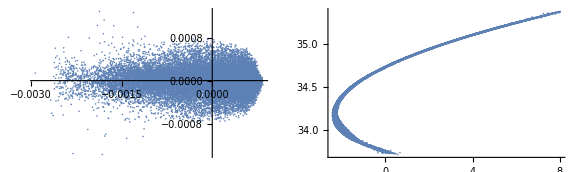

```mathematica
GraphicsGrid[{{ListPlot[{Transpose[{x-Mean[x],y}]},PlotRange->All],ListPlot[{Transpose[{10^12(t-Mean[t]),0.511p}]},PlotRange->All]}},ImageSize->Large]
```

```mathematica
sddsInterpret["C:\\anaconda32\\Work\\OnlineModel\\SimulationFramework\\Examples\\CLARA_BA1\\"<>dir<>"\\EBT-BA1-COFFIN-FOC.SDDS"]
```

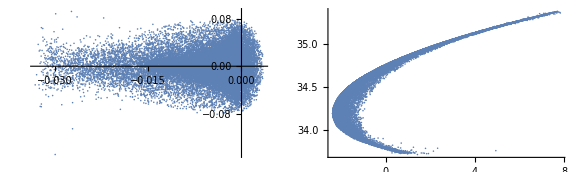

```mathematica
GraphicsGrid[{{ListPlot[{Transpose[{x,y}]},PlotRange->All],ListPlot[{Transpose[{10^12(t-Mean[t]),0.511p}]},PlotRange->All]}},ImageSize->Large]
```

```mathematica
sddsInterpret["C:\\anaconda32\\Work\\OnlineModel\\SimulationFramework\\Examples\\CLARA_BA1\\"<>dir<>"\\S02.twi",SDDSVerbose->True]
```

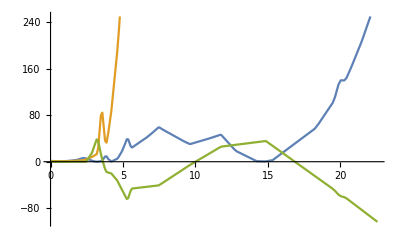

```mathematica
ListLinePlot[{Transpose[{s,betax}],Transpose[{s,betay}],Transpose[{s,100etax}]},PlotRange->{All,{Automatic,250}}]
```

```mathematica
sddsInterpret["C:\\anaconda32\\Work\\OnlineModel\\SimulationFramework\\Examples\\CLARA_BA1\\"<>dir<>"\\S02.sig",sddsVerbose->True]
```

Number of Pages: 1;	Current Page(s): {1}

Variables (Re)Assigned: {s, ElementName, ElementOccurence, ElementType, s1, s12, s13, s14, s15, s16, s17, s2, s23, s24, s25, s26, s27, s3, s34, s35, s36, s37, s4, s45, s46, s47, s5, s56, s57, s6, s67, s7, ma1, ma2, ma3, ma4, ma5, ma6, ma7, minimum1, minimum2, minimum3, minimum4, minimum5, minimum6, minimum7, maximum1, maximum2, maximum3, maximum4, maximum5, maximum6, maximum7, Sx, Sxp, Sy, Syp, Ss, Sdelta, St, ex, enx, ecx, ecnx, ey, eny, ecy, ecny, betaxBeam, alphaxBeam, betayBeam, alphayBeam}

Parameters (Re)Assigned: {Step}

```mathematica
ListLinePlot[{Transpose[{s,10^3 Sx}],Transpose[{s,10^3 Sy}]}]
```

-Graphics-

```mathematica
ListLinePlot[{Transpose[{s,10^6 enx}],Transpose[{s,10^6 eny}]}]
```

-Graphics-

```mathematica
ListLinePlot[{Transpose[{s,betaxBeam}],Transpose[{s,betayBeam}],Transpose[{s,100000s16}]}]
```

-Graphics-

## ASTRA (Bruno)

```mathematica
<<ASTRAInterpret`
```

```mathematica
dir="ASTRA";
```

```mathematica
ASTRABeamInterpret["\\\\apclara1\\jkj62\\Github\\OnlineModel\\SimulationFramework\\Examples\\CLARA_BA1\\"<>dir<>"\\S02.2443.001",ASTRAVerbose->True]
```

Columns Redefined: x [m], y [m], z [m], px [eV/c], py [eV/c], pz [eV/c], clock [ns], charge [nC], index [DimensionlessUnit], status [DimensionlessUnit]

```mathematica
ListPlot[{Transpose[{x-Mean[x],y}]},PlotRange->All]
```

-Graphics-

```mathematica
speedoflight=QuantityMagnitude[UnitConvert[Quantity["SpeedOFlight"]]]
```

299792458

```mathematica
ListPlot[{Transpose[{-10^12(z-Mean[z])/speedoflight,10^-6 pz}]},PlotRange->All]
```

-Graphics-

```mathematica
files=Sort[FileNames["\\\\apclara1\\jkj62\\Github\\OnlineModel\\SimulationFramework\\Examples\\CLARA_BA1\\"<>dir<>"\\*.Xemit.001"],FileDate[#1]<FileDate[#2]&]
```

{\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\ASTRA\S02.Xemit.001,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\ASTRA\C2V.Xemit.001,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\ASTRA\VELA.Xemit.001,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\ASTRA\BA1.Xemit.001,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\ASTRA\BA1_dipole.Xemit.001}

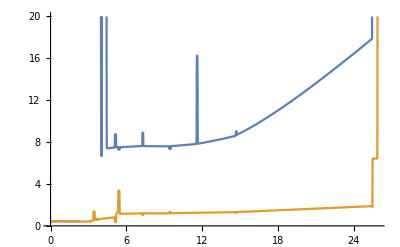

```mathematica
offset=0;
Show[Block[{},
ASTRAemitInterpret[#,ASTRAVerbose->False];
plot=ListLinePlot[{Transpose[{offset+z-z[[1]],ϵxnorm}],Transpose[{offset+z-z[[1]],ϵynorm}]},PlotRange->{All,{0,20}}];
offset=offset+z[[-1]]-z[[1]];
plot
]&/@files,PlotRange->All]
```

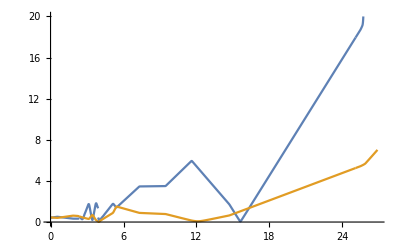

```mathematica
offset=0;
Show[Block[{},
ASTRAemitInterpret[#,ASTRAVerbose->False];
plot=ListLinePlot[{Transpose[{offset+z-z[[1]],xrms}],Transpose[{offset+z-z[[1]],yrms}]},PlotRange->{All,{0,20}}];
offset=offset+z[[-1]]-z[[1]];
plot
]&/@files,PlotRange->All]
```

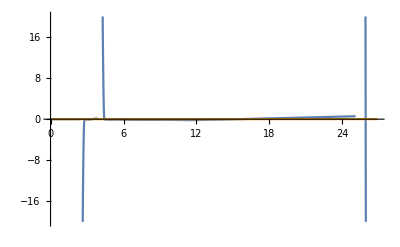

```mathematica
offset=0;
Show[Block[{},
ASTRAemitInterpret[#,ASTRAVerbose->False];
plot=ListLinePlot[{Transpose[{offset+z-z[[1]],xavr}],Transpose[{offset+z-z[[1]],yavr}]},PlotRange->{All,{-20,20}}];
offset=offset+z[[-1]]-z[[1]];
plot
]&/@files,PlotRange->All]
```